Bee Specialization Model 
First set up the basic equations for just native plants and specialist bees

```mathematica
(*NativePlant[D_]:=rmax*D*(1-(D/Kd))*)
NativePollen[n_]:= D*ϕ - (1/Ys)*((Us*n*s)/(1+Us*hs*n))
SpecialistBee[s_]:= (((Us*n*s)/(1+Us*hs*n)) - ms*n)
(*NativePlantBeesMax[Dx_]:= rmax*1* Dx(1-(Dx/Kd))
NativePlantBeesMin[Dn_]:=rmax*(G/xreq)*Dn(1-(Dn/Kd))*)
NativePlant[d_] := rmax Min[1, (s δ)/xreq] d(1-(d/kd))
NativePlantModified[dm_]:= rmax(c E ^(a x))/(c E ^(a x) + (1-c))dm(1-(dm/kd)) (*This is a variant that describes the amount of bees (x) contributing to the pollination of the plants being an S shape curve rather than a linear relationship, which might be more biologically relevant*)
```

```mathematica
Solve[NativePlant[D]==0∧NativePollen[N]==0∧SpecialistBee[S]==0,{D, N, S}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{D→0,S→0},{D→0,N→-ms/((-1+hs ms) Us),S→0},{D→Kd,N→-ms/((-1+hs ms) Us),S→(Kd Ys ϕ)/ms}}

```mathematica
Solve[NativePlantBeesMax[Dx]==0∧NativePollen[N]==0∧SpecialistBee[S]==0,{Dx, N, S}]
```

{{Dx→0,N→-ms/((-1+hs ms) Us),S→(D Ys ϕ)/ms},{Dx→Kd,N→-ms/((-1+hs ms) Us),S→(D Ys ϕ)/ms}}

```mathematica
Solve[NativePlantBeesMin[Dn]==0∧NativePollen[N]==0∧SpecialistBee[S]==0,{Dn, N, S}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Dn→0,S→0},{Dn→0,N→-ms/((-1+hs ms) Us),S→0},{Dn→Kd,N→-ms/((-1+hs ms) Us),S→(Kd Ys ϕ)/ms}}

```mathematica
Solve[NativePollen[N]==0∧NativePlant[D]==0,{N,D}](*With just pollen and native plant are present in the system, which doesn't really make sense?*)
```

{{N→0,D→0},{N→(Kd Ys ϕ)/(Us (S-hs Kd Ys ϕ)),D→Kd}}

```mathematica
Solve[NativePollen[N], N]
```

Solve::naqs: NativePollen[N] is not a quantified system of equations and inequalities.

Solve[NativePollen[N],N]

# Solving For Equilibria

First for Native Plant

```mathematica
Clear[rmax, Kd]
Solve[NativePlant[d]==0,d]
Solve[NativePlant[d] == 0 ∧ NativePollen[N] == 0,{d,N}]
Solve[NativePlant[d] == 0 ∧NativePollen[N] == 0∧SpecialistBee[S]==0, {d,N,S} ]
```

{{d→0},{d→kd}}

{{d→0,N→(D Ys ϕ)/(Us (s-D hs Ys ϕ))},{d→kd,N→(D Ys ϕ)/(Us (s-D hs Ys ϕ))}}

{{d→0,N→(D Ys ϕ)/(Us (s-D hs Ys ϕ)),S→(ms+hs ms n Us)/Us},{d→kd,N→(D Ys ϕ)/(Us (s-D hs Ys ϕ)),S→(ms+hs ms n Us)/Us}}

For Native Pollen

```mathematica
Clear[phi, Ys, Us, hs]
Solve[NativePollen[N] == 0, {N,S}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{S→(D (1+hs N Us) Ys ϕ)/(N Us)}}

For Specialist Bee

```mathematica
Clear[ms]
Solve[SpecialistBee[S]==0, S]
```

{{S→0}}

## Run some simulations

```mathematica
Clear[n,d]
```

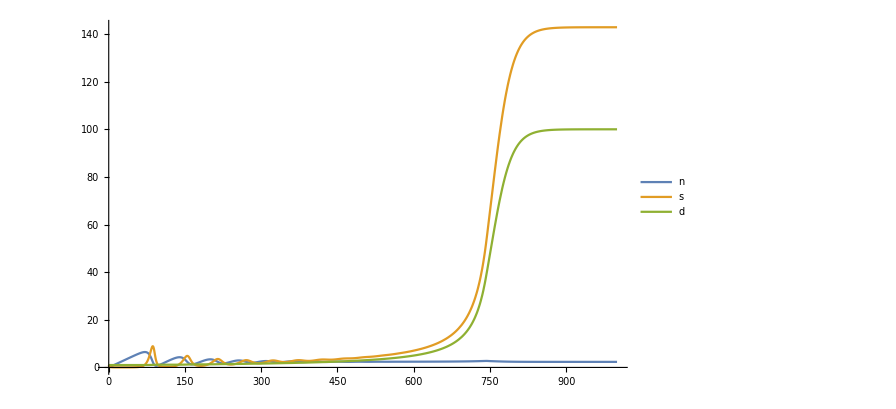

{{n→InterpolatingFunction[…],s→InterpolatingFunction[…],d→InterpolatingFunction[…]}}

```mathematica
pars = {ϕ -> 10, Ys -> 0.1, Us -> 0.01, hs -> 1, ms -> 0.7, r->0.05, Kd -> 100, n0 -> 0, s0 -> 1, d0 -> 1, xreq -> 100, δ ->2};
tmax = 1000;

sim [pars_]:=NDSolve[
{n'[t]==d[t]ϕ - (1/Ys)((Us*n[t]*s[t])/(1+Us*hs*n[t])),
s'[t] == (((Us*n[t]*s[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == r *Min[1,(s[t] δ )/xreq]*d[t](1-(d[t]/(Kd))),
n[0 ]== n0, 
s[0]==s0,
d[0]==d0}/.pars,
{n,s,d}, 
{t, 0, tmax}]
sol = sim[pars];
Plot[{n[t]/100/.sol, s[t]/.sol, d[t] /. sol}, {t,0,tmax}, PlotLegends -> {n,s,d}, PlotRange -> All]
```

Looking at the full model with the parameters we have

{{n→InterpolatingFunction[…],s→InterpolatingFunction[…],d→InterpolatingFunction[…],a→InterpolatingFunction[…],e→InterpolatingFunction[…],g→InterpolatingFunction[…]}}

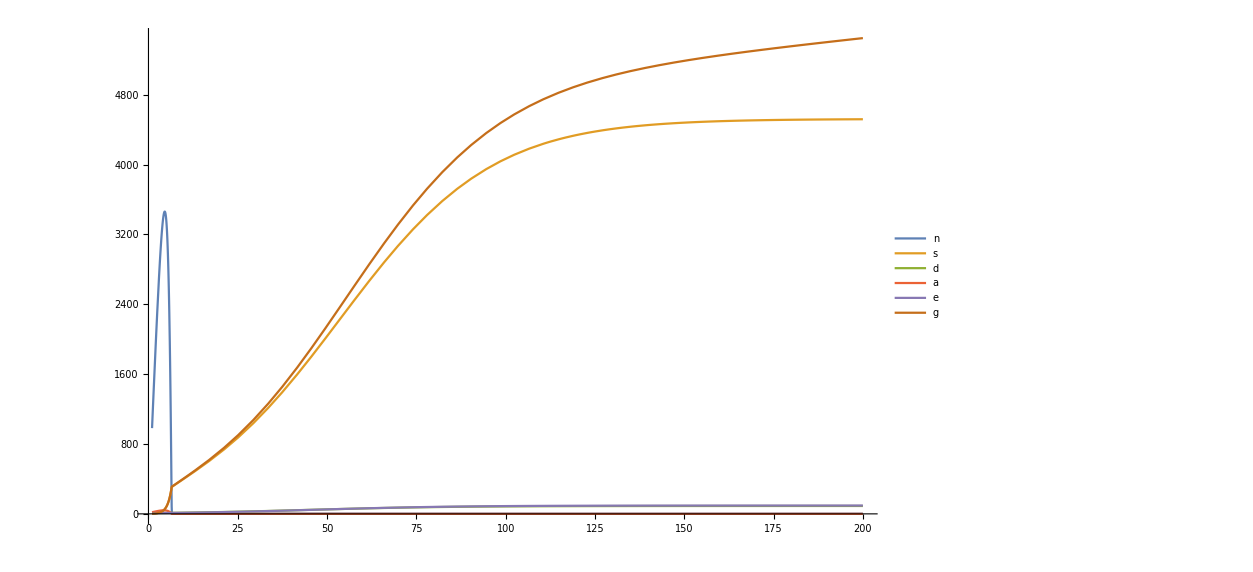

```mathematica
Clear[ϕ, Ys, Us, hs, ms, r, Kd, Ke, Yg, Ug, hg, mg, β, α, xreq, n0, s0, d0, g0, e0, a0]; 
pars2 = {ϕ -> 100, Ys -> 0.05, Us -> 0.05, hs -> 1, ms -> 0.1, r->0.05, Kd -> 100,Ke -> 100, Yg -> 0.05, Ug -> 0.05, hg ->1, mg ->0.1, β ->0.1, α -> 0.05,xreq -> 100,  n0 -> 10, s0 -> 1, d0 -> 10, g0 -> 1, e0 -> 10, a0 -> 10,δ->2};
tmax2= 200;

sim2 [pars2_]:=NDSolve[
{n'[t]==d[t]ϕ - (1/Ys)((Us*n[t]*s[t])/(1+Us*hs*n[t])),
a'[t] == e[t] - (1/Yg)((Ug a[t] g[t])/(1 + Ug hg n[t]+ Ug hg a[t])),
g'[t] == (g[t] (Ug a[t]+ Ug n[t])/(1 + Ug hg n[t] + Ug hg a[t])) - mg g[t], 
s'[t] == (((Us*n[t]*s[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == r(Min[1,(s[t] δ + g[t])/xreq])d[t](Kd - d[t] - β e[t])/Kd,
e'[t] ==  r(Min[1,( g[t])/xreq]) e[t](Ke - e[t] - α d[t])/Ke,
n[0 ]== n0, 
s[0]==s0,
d[0]==d0,
a[0]==a0,
e[0]==e0,
g[0]==g0}/.pars2,
{n,s,d, a, e, g}, 
{t, 1, tmax2}]
sol2 = sim2[pars2]
Plot[{n[t]/.sol2, s[t]/.sol2, d[t] /. sol2,  a[t] /. sol2, e[t] /. sol2 ,  g[t] /. sol2},{t,1,tmax2}, PlotLegends -> {n,s,d,a,e,g}, PlotRange -> All]
```

### Looking at editing r max for bees

```mathematica
?Min
```

{{n→InterpolatingFunction[…],s→InterpolatingFunction[…],d→InterpolatingFunction[…]}}

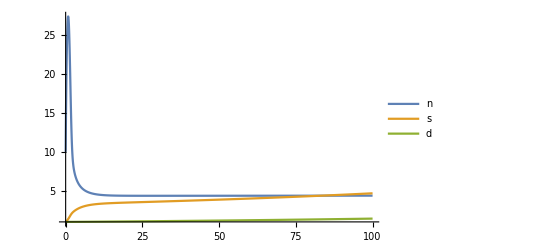

```mathematica
Clear[ϕ, Ys, Us, hs, ms, rmax, Kd, n0, s0, d0, δ, x]
pars = {ϕ -> 100, Ys -> 0.01, Us -> 0.1, hs -> 1, ms -> 0.3, rmax->0.05, Kd -> 15, n0 -> 10, s0 -> 1, d0 ->1, δ -> 2, x -> 100};
tmax = 100;


simulate[parsimon_]:=NDSolve[
{n'[t]==d[t]ϕ - (1/Ys)((Us*n[t]*s[t])/(1+Us*hs*n[t])),
s'[t] == (((Us*n[t]*s[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == (rmax*Min[1, (s[t] δ)/x ])* d[t](1-(d[t]/Kd)),
n[0 ]== n0, 
s[0]==s0,
d[0]==d0}/.parsimon,
{n,s,d}, 
{t, 0, tmax}]
solution = simulate[pars]
Plot[{n[t]/.solution, s[t]/.solution, d[t] /. solution}, {t,0,tmax}, PlotLegends -> {n,s,d}, PlotRange -> All]
```

```mathematica
(*the sliders! single species logistic growth*)
Clear[n0,s0, d0, Us, hs, ms, Kd, t, δ, xreq, Ys ]
pars2 = {ϕ -> 100, Ys -> 0.01, Us -> 0.1, hs -> 1, ms -> 0.7, Kd -> 100,Ke -> 100, Yg -> 0.005, Ug -> 0.05, hg ->1, mg ->0.7, xreq -> 100,  n0 -> 10, s0 -> 1, d0 -> 1, g0 -> 1, e0 -> 1, a0 -> 10,δ->2};
Manipulate[
(*make a module to localize variables*)
Module[{slv},
(*solve ODES*)
slv=NDSolve[
(*equations*)
{
(*ODE*)
n'[t]==d[t]ϕ - (1/Ys)((Us*n[t]*s[t])/(1+Us*hs*n[t])),
s'[t] == (((Us*n[t]*s[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == r *Min[1,(s[t] δ )/xreq]*d[t](1-(d[t]/(Kd))),
n[0 ]== n0, 
s[0]==s0,
d[0]==d0 
},
(*state variable(s)*)
{n,s,d},
(*independent variable: time*)
{t,0,tmax}
];
(*output*)
Plot[n[t]/.slv,s[t]/.slv,d[t]/.slv,{t,0,tmax}]
],
(*sliders*)
{{ϕ, 0.1}}
{{r,.05},0,1}

]
```

ReplaceAll::reps: {pars2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2 in the first argument {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2.

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$4214,s[t]/.slv$4214,d[t]/.slv$4214,{t,0,tmax}]. An option must be a rule or a list of rules.

ReplaceAll::reps: {pars2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2 in the first argument {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2.

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$6338,s[t]/.slv$6338,d[t]/.slv$6338,{t,0,tmax}]. An option must be a rule or a list of rules.

ReplaceAll::reps: {pars2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2 in the first argument {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2.

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$9312,s[t]/.slv$9312,d[t]/.slv$9312,{t,0,tmax}]. An option must be a rule or a list of rules.

ReplaceAll::reps: {pars2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2 in the first argument {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2.

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$9857,s[t]/.slv$9857,d[t]/.slv$9857,{t,0,tmax}]. An option must be a rule or a list of rules.

ReplaceAll::reps: {pars2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2 in the first argument {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2.

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$7365,s[t]/.slv$7365,d[t]/.slv$7365,{t,0,tmax}]. An option must be a rule or a list of rules.

ReplaceAll::reps: {pars2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2 in the first argument {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2.

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$8646,s[t]/.slv$8646,d[t]/.slv$8646,{t,0,tmax}]. An option must be a rule or a list of rules.

ReplaceAll::reps: {pars2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2 in the first argument {n'[t]==ϕ d[t]-(Us n[t] s[t])/(Ys (1+Times[«3»])),s'[t]==-ms s[t]+(Us n[t] s[t])/(1+Times[«3»]),d'[t]==0.05 d[t] (1-d[t]/Kd) Min[1,(δ s[t])/xreq],n[0]==n0,s[0]==s0,d[0]==d0}/.pars2.

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$4508,s[t]/.slv$4508,d[t]/.slv$4508,{t,0,tmax}]. An option must be a rule or a list of rules.

NDSolve::ndnl: Endpoint tmax in {t,0.,tmax} is not a real number.

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$9076,s[t]/.slv$9076,d[t]/.slv$9076,{t,0,tmax}]. An option must be a rule or a list of rules.

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$17066,s[t]/.slv$17066,d[t]/.slv$17066,{t,0,tmax}]. An option must be a rule or a list of rules.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ dm[t].

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$19054,s[t]/.slv$19054,d[t]/.slv$19054,{t,0,tmax}]. An option must be a rule or a list of rules.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ dm[t].

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$21282,s[t]/.slv$21282,d[t]/.slv$21282,{t,0,tmax}]. An option must be a rule or a list of rules.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ dm[t].

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[n[t]/.slv$22334,s[t]/.slv$22334,d[t]/.slv$22334,{t,0,tmax}]. An option must be a rule or a list of rules.

Syntax::tsntxi: "Module{s},s=NDSolve" is incomplete; more input is needed.

```mathematica
DynamicModule[{eqns,init,sol,n,s,d,t},
Manipulate[
eqns={n'[t]==d[t]ϕ - (1/Ys)((Us*n[t]*s[t])/(1+Us*hs*n[t])),s'[t] == (((Us*n[t]*s[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == (rmax*Min[1, (s[t] δ)/x ])* d[t](1-(d[t]/Kd))};
init={n[0]==n0,s[0]==s0,d[0]==d0};
sol=NDSolve[{eqns,init},{n,s,d},{t,0,100}];
Plot[Evaluate[{n[t],s[t],d[t]}/. sol],{t,0,100},PlotLegends->Placed[{"n[t]","s[t]","d[t]"},Scaled[{0.9,0.5}]]],
{{rmax,.05},0.01,1},
{{phi,100},1,1000},
{{Ys,1},0.01,1},
{{Us,1},0.01,1},
{{hs,1},0.01,100},
{{ms,.8},0.01,1},
{{δ,2},1,10},
{{x,100},1,10000},
{{Kd,10},1,100},
Delimiter,"initial conditions",
{{n0,10},1,100},
{{s0,10},1,10},
{{d0,10},1,10}]]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$484 == 0..

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$484 == 0..

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$38 == 0..

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$38 == 0..

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$38 == 0..

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$23 == 0..

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],«1»,FE`d$$23'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$23[0.00204286] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{«1»},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+«1»,FE`d$$23'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$23[0.00204286] Min[1.,Times[«2»]]},{«1»}},«1»,{«21»,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$23 == 0..

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],«1»,FE`d$$23'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$23[0.00204286] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{«1»},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+«1»,FE`d$$23'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$23[0.00204286] Min[1.,Times[«2»]]},{«1»}},«1»,{«21»,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$23 == 0..

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$38 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$38'[FE`t$$38]==ϕ FE`d$$38[«1»]-10. Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`s$$38'[FE`t$$38]==-0.3 FE`s$$38[«1»]+0.1 Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`d$$38'[FE`t$$38]==0.05 (1+Times[«2»]) FE`d$$38[FE`t$$38] Min[1,Times[«2»]]},{FE`n$$38[0]==10,FE`s$$38[0]==1,FE`d$$38[0]==1}},{FE`n$$38,FE`s$$38,FE`d$$38},{FE`t$$38,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$38 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$38'[FE`t$$38]==ϕ FE`d$$38[«1»]-10. Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`s$$38'[FE`t$$38]==-0.3 FE`s$$38[«1»]+0.1 Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`d$$38'[FE`t$$38]==0.05 (1+Times[«2»]) FE`d$$38[FE`t$$38] Min[1,Times[«2»]]},{FE`n$$38[0]==10,FE`s$$38[0]==1,FE`d$$38[0]==1}},{FE`n$$38,FE`s$$38,FE`d$$38},{FE`t$$38,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$38'[0.00204286]==ϕ FE`d$$38[«1»]-10. Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`s$$38'[0.00204286]==-0.3 FE`s$$38[«1»]+0.1 Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`d$$38'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$38[0.00204286] Min[1,Times[«2»]]},{FE`n$$38[0]==10,FE`s$$38[0]==1,FE`d$$38[0]==1}},{FE`n$$38,FE`s$$38,FE`d$$38},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$38'[0.00204286]==ϕ FE`d$$38[«1»]-10. Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`s$$38'[0.00204286]==-0.3 FE`s$$38[«1»]+0.1 Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`d$$38'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$38[0.00204286] Min[1.,Times[«2»]]},{FE`n$$38[0.]==10.,FE`s$$38[0.]==1.,FE`d$$38[0.]==1.}},{FE`n$$38,FE`s$$38,FE`d$$38},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$38 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$38'[FE`t$$38]==ϕ FE`d$$38[«1»]-10. Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`s$$38'[FE`t$$38]==-0.3 FE`s$$38[«1»]+0.1 Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`d$$38'[FE`t$$38]==0.05 (1+Times[«2»]) FE`d$$38[FE`t$$38] Min[1,Times[«2»]]},{FE`n$$38[0]==10,FE`s$$38[0]==1,FE`d$$38[0]==1}},{FE`n$$38,FE`s$$38,FE`d$$38},{FE`t$$38,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$38 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$38'[FE`t$$38]==ϕ FE`d$$38[«1»]-10. Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`s$$38'[FE`t$$38]==-0.3 FE`s$$38[«1»]+0.1 Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`d$$38'[FE`t$$38]==0.05 (1+Times[«2»]) FE`d$$38[FE`t$$38] Min[1,Times[«2»]]},{FE`n$$38[0]==10,FE`s$$38[0]==1,FE`d$$38[0]==1}},{FE`n$$38,FE`s$$38,FE`d$$38},{FE`t$$38,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$38'[0.00204286]==ϕ FE`d$$38[«1»]-10. Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`s$$38'[0.00204286]==-0.3 FE`s$$38[«1»]+0.1 Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`d$$38'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$38[0.00204286] Min[1,Times[«2»]]},{FE`n$$38[0]==10,FE`s$$38[0]==1,FE`d$$38[0]==1}},{FE`n$$38,FE`s$$38,FE`d$$38},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$38'[0.00204286]==ϕ FE`d$$38[«1»]-10. Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`s$$38'[0.00204286]==-0.3 FE`s$$38[«1»]+0.1 Power[«2»] FE`n$$38[«1»] FE`s$$38[«1»],FE`d$$38'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$38[0.00204286] Min[1.,Times[«2»]]},{FE`n$$38[0.]==10.,FE`s$$38[0.]==1.,FE`d$$38[0.]==1.}},{FE`n$$38,FE`s$$38,FE`d$$38},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$38 == 0..

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$23 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[FE`t$$23]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[FE`t$$23]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[FE`t$$23]==0.05 (1+Times[«2»]) FE`d$$23[FE`t$$23] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{FE`t$$23,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$23[0.00204286] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$23[0.00204286] Min[1.,Times[«2»]]},{FE`n$$23[0.]==10.,FE`s$$23[0.]==1.,FE`d$$23[0.]==1.}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$23 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[FE`t$$23]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[FE`t$$23]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[FE`t$$23]==0.05 (1+Times[«2»]) FE`d$$23[FE`t$$23] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{FE`t$$23,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$23[0.00204286] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$23[0.00204286] Min[1.,Times[«2»]]},{FE`n$$23[0.]==10.,FE`s$$23[0.]==1.,FE`d$$23[0.]==1.}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$23 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[FE`t$$23]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[FE`t$$23]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[FE`t$$23]==0.05 (1+Times[«2»]) FE`d$$23[FE`t$$23] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{FE`t$$23,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$23[0.00204286] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$23[0.00204286] Min[1.,Times[«2»]]},{FE`n$$23[0.]==10.,FE`s$$23[0.]==1.,FE`d$$23[0.]==1.}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$23 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[FE`t$$23]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[FE`t$$23]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[FE`t$$23]==0.05 (1+Times[«2»]) FE`d$$23[FE`t$$23] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{FE`t$$23,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$23[0.00204286] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$23[0.00204286] Min[1.,Times[«2»]]},{FE`n$$23[0.]==10.,FE`s$$23[0.]==1.,FE`d$$23[0.]==1.}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$23 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[FE`t$$23]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[FE`t$$23]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[FE`t$$23]==0.05 (1+Times[«2»]) FE`d$$23[FE`t$$23] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{FE`t$$23,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$23[0.00204286] Min[1,Times[«2»]]},{FE`n$$23[0]==10,FE`s$$23[0]==1,FE`d$$23[0]==1}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$23'[0.00204286]==ϕ FE`d$$23[«1»]-10. Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`s$$23'[0.00204286]==-0.3 FE`s$$23[«1»]+0.1 Power[«2»] FE`n$$23[«1»] FE`s$$23[«1»],FE`d$$23'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$23[0.00204286] Min[1.,Times[«2»]]},{FE`n$$23[0.]==10.,FE`s$$23[0.]==1.,FE`d$$23[0.]==1.}},{FE`n$$23,FE`s$$23,FE`d$$23},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$23 == 0..

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$33 == 0..

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$33'[0.00204286]==ϕ FE`d$$33[«1»]-10. Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],FE`s$$33'[«21»]==«1»,FE`d$$33'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$33[0.00204286] Min[1,Times[«2»]]},{«1»}},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$33'[0.00204286]==ϕ FE`d$$33[«1»]-10. Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],«8»'[«21»]==«1»,FE`d$$33'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$33[0.00204286] Min[1.,Times[«2»]]},{«1»}},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$33 == 0..

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$33'[0.00204286]==ϕ FE`d$$33[«1»]-10. Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],FE`s$$33'[«21»]==«1»,FE`d$$33'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$33[0.00204286] Min[1,Times[«2»]]},{«1»}},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$33'[0.00204286]==ϕ FE`d$$33[«1»]-10. Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],«8»'[«21»]==«1»,FE`d$$33'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$33[0.00204286] Min[1.,Times[«2»]]},{«1»}},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$33 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$33'[FE`t$$33]==ϕ FE`d$$33[«1»]-10. Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],FE`s$$33'[FE`t$$33]==-0.3 FE`s$$33[«1»]+0.1 Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],FE`d$$33'[FE`t$$33]==0.05 (1+Times[«2»]) FE`d$$33[FE`t$$33] Min[1,Times[«2»]]},{FE`n$$33[0]==10,FE`s$$33[0]==1,FE`d$$33[0]==1}},{FE`n$$33,FE`s$$33,FE`d$$33},{FE`t$$33,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$33'[0.00204286]==ϕ FE`d$$33[«1»]-10. Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],FE`s$$33'[0.00204286]==-0.3 FE`s$$33[«1»]+0.1 Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],FE`d$$33'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$33[0.00204286] Min[1,Times[«2»]]},{FE`n$$33[0]==10,FE`s$$33[0]==1,FE`d$$33[0]==1}},{FE`n$$33,FE`s$$33,FE`d$$33},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$33'[0.00204286]==ϕ FE`d$$33[«1»]-10. Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],FE`s$$33'[0.00204286]==-0.3 FE`s$$33[«1»]+0.1 Power[«2»] FE`n$$33[«1»] FE`s$$33[«1»],FE`d$$33'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$33[0.00204286] Min[1.,Times[«2»]]},{FE`n$$33[0.]==10.,FE`s$$33[0.]==1.,FE`d$$33[0.]==1.}},{FE`n$$33,FE`s$$33,FE`d$$33},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$33 == 0..

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$22 == 0..

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$22 == 0..

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$22 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$22'[FE`t$$22]==ϕ FE`d$$22[«1»]-10. Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`s$$22'[FE`t$$22]==-0.3 FE`s$$22[«1»]+0.1 Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`d$$22'[FE`t$$22]==0.05 (1+Times[«2»]) FE`d$$22[FE`t$$22] Min[1,Times[«2»]]},{FE`n$$22[0]==10,FE`s$$22[0]==1,FE`d$$22[0]==1}},{FE`n$$22,FE`s$$22,FE`d$$22},{FE`t$$22,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$22'[0.00204286]==ϕ FE`d$$22[«1»]-10. Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`s$$22'[0.00204286]==-0.3 FE`s$$22[«1»]+0.1 Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`d$$22'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$22[0.00204286] Min[1,Times[«2»]]},{FE`n$$22[0]==10,FE`s$$22[0]==1,FE`d$$22[0]==1}},{FE`n$$22,FE`s$$22,FE`d$$22},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$22'[0.00204286]==ϕ FE`d$$22[«1»]-10. Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`s$$22'[0.00204286]==-0.3 FE`s$$22[«1»]+0.1 Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`d$$22'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$22[0.00204286] Min[1.,Times[«2»]]},{FE`n$$22[0.]==10.,FE`s$$22[0.]==1.,FE`d$$22[0.]==1.}},{FE`n$$22,FE`s$$22,FE`d$$22},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$22 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$22'[FE`t$$22]==ϕ FE`d$$22[«1»]-10. Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`s$$22'[FE`t$$22]==-0.3 FE`s$$22[«1»]+0.1 Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`d$$22'[FE`t$$22]==0.05 (1+Times[«2»]) FE`d$$22[FE`t$$22] Min[1,Times[«2»]]},{FE`n$$22[0]==10,FE`s$$22[0]==1,FE`d$$22[0]==1}},{FE`n$$22,FE`s$$22,FE`d$$22},{FE`t$$22,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$22'[0.00204286]==ϕ FE`d$$22[«1»]-10. Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`s$$22'[0.00204286]==-0.3 FE`s$$22[«1»]+0.1 Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`d$$22'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$22[0.00204286] Min[1,Times[«2»]]},{FE`n$$22[0]==10,FE`s$$22[0]==1,FE`d$$22[0]==1}},{FE`n$$22,FE`s$$22,FE`d$$22},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$22'[0.00204286]==ϕ FE`d$$22[«1»]-10. Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`s$$22'[0.00204286]==-0.3 FE`s$$22[«1»]+0.1 Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`d$$22'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$22[0.00204286] Min[1.,Times[«2»]]},{FE`n$$22[0.]==10.,FE`s$$22[0.]==1.,FE`d$$22[0.]==1.}},{FE`n$$22,FE`s$$22,FE`d$$22},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$22 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$22'[FE`t$$22]==ϕ FE`d$$22[«1»]-10. Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`s$$22'[FE`t$$22]==-0.3 FE`s$$22[«1»]+0.1 Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`d$$22'[FE`t$$22]==0.05 (1+Times[«2»]) FE`d$$22[FE`t$$22] Min[1,Times[«2»]]},{FE`n$$22[0]==10,FE`s$$22[0]==1,FE`d$$22[0]==1}},{FE`n$$22,FE`s$$22,FE`d$$22},{FE`t$$22,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$22'[0.00204286]==ϕ FE`d$$22[«1»]-10. Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`s$$22'[0.00204286]==-0.3 FE`s$$22[«1»]+0.1 Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`d$$22'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$22[0.00204286] Min[1,Times[«2»]]},{FE`n$$22[0]==10,FE`s$$22[0]==1,FE`d$$22[0]==1}},{FE`n$$22,FE`s$$22,FE`d$$22},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$22'[0.00204286]==ϕ FE`d$$22[«1»]-10. Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`s$$22'[0.00204286]==-0.3 FE`s$$22[«1»]+0.1 Power[«2»] FE`n$$22[«1»] FE`s$$22[«1»],FE`d$$22'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$22[0.00204286] Min[1.,Times[«2»]]},{FE`n$$22[0.]==10.,FE`s$$22[0.]==1.,FE`d$$22[0.]==1.}},{FE`n$$22,FE`s$$22,FE`d$$22},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$22 == 0..

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$186 == 0..

ReplaceAll::reps: {NDSolve[{{FE`n$$186'[FE`t$$186]==ϕ FE`d$$186[«1»]-10. Power[«2»] FE`n$$186[«1»] FE`s$$186[«1»],FE`s$$186'[FE`t$$186]==-0.3 FE`s$$186[«1»]+0.1 Power[«2»] FE`n$$186[«1»] FE`s$$186[«1»],FE`d$$186'[FE`t$$186]==0.05 (1+Times[«2»]) FE`d$$186[FE`t$$186] Min[1,Times[«2»]]},{FE`n$$186[0]==10,FE`s$$186[0]==1,FE`d$$186[0]==1}},{FE`n$$186,FE`s$$186,FE`d$$186},{FE`t$$186,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$186'[0.00204286]==ϕ FE`d$$186[«1»]-10. Power[«2»] FE`n$$186[«1»] FE`s$$186[«1»],FE`s$$186'[0.00204286]==-0.3 FE`s$$186[«1»]+0.1 Power[«2»] FE`n$$186[«1»] FE`s$$186[«1»],FE`d$$186'[0.00204286]==0.05 (1+Times[«2»]) FE`d$$186[0.00204286] Min[1,Times[«2»]]},{FE`n$$186[0]==10,FE`s$$186[0]==1,FE`d$$186[0]==1}},{FE`n$$186,FE`s$$186,FE`d$$186},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{FE`n$$186'[0.00204286]==ϕ FE`d$$186[«1»]-10. Power[«2»] FE`n$$186[«1»] FE`s$$186[«1»],FE`s$$186'[0.00204286]==-0.3 FE`s$$186[«1»]+0.1 Power[«2»] FE`n$$186[«1»] FE`s$$186[«1»],FE`d$$186'[0.00204286]==0.05 (1.+Times[«2»]) FE`d$$186[0.00204286] Min[1.,Times[«2»]]},{FE`n$$186[0.]==10.,FE`s$$186[0.]==1.,FE`d$$186[0.]==1.}},{FE`n$$186,FE`s$$186,FE`d$$186},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$186 == 0..

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$455 == 0..

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at FE`t$$455 == 0..

(1-D/Kd) rmax-(D rmax)/Kd

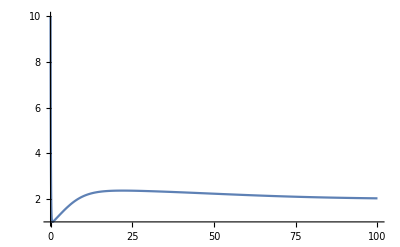
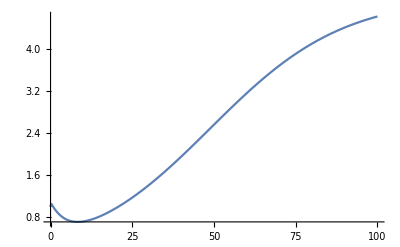
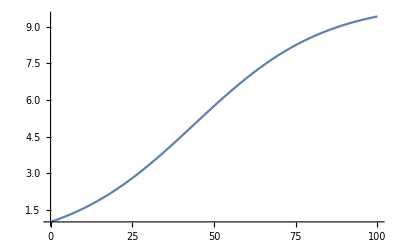

-Graphics-

```mathematica
Plot[Evaluate[#[t]/.sol], {t, 0, tmax}, PlotRange -> All] & /@{n, s, d}

plot[pars_] :=Module[{sol},
sol=sim[pars];
 GraphicsColumn[{
Plot[Evaluate[n[t]/.sol], {t, 0, tmax},PlotLegends -> {n}, PlotStyle -> Orange,  PlotRange -> All],
Plot[Evaluate[s[t]/.sol], {t, 0, tmax}, PlotLegends -> {s},PlotStyle -> Purple,PlotRange -> All],
Plot[Evaluate[d[t]/.sol], {t, 0, tmax},PlotLegends -> {d},PlotStyle -> Green, PlotRange -> All]}]]
plot[pars]
```

Alternate Functional Form

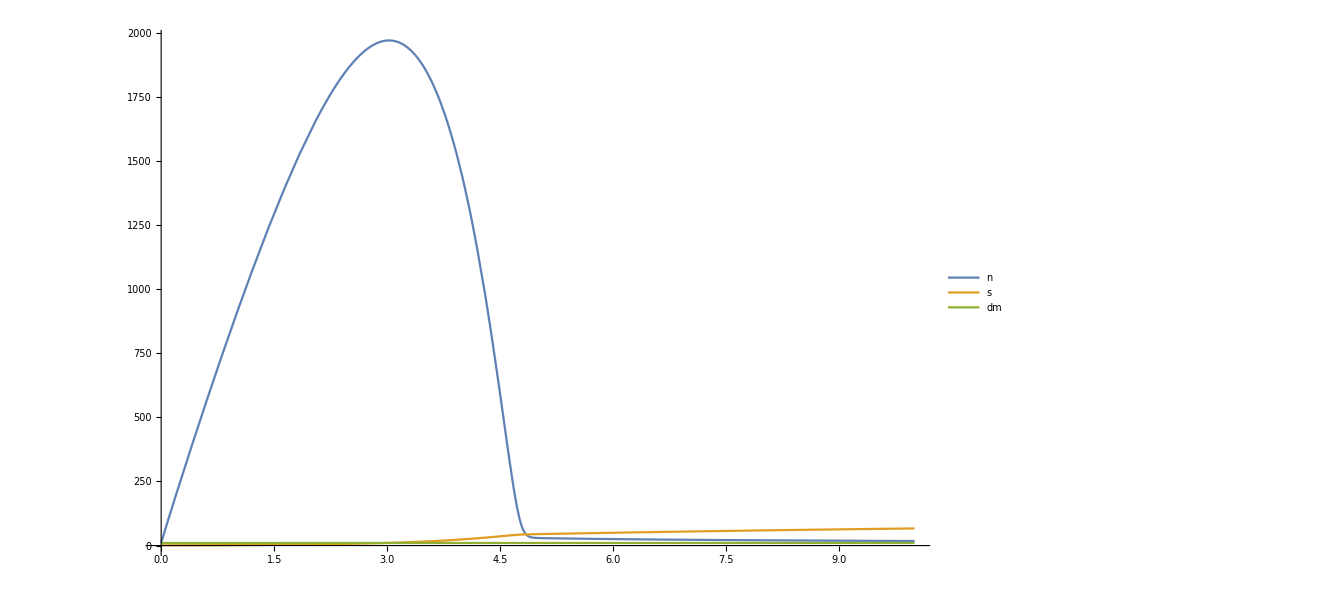

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ dm[t].

Hold[clear[n,s,d]]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ dm[t].

Hold[n=dm[t] ϕ-(Us n[t] s[t])/(Ys (1+Us hs n[t]))]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ dm[t].

Hold[s=(Us n[t] s[t])/(1+Us hs n[t])-ms s[t]]

(c ⅇ^(a dm[t]) rmax dm[t] (1-dm[t]/Kd))/(1-c+c ⅇ^(a dm[t]))

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ dm[t].

Hold[eqns={n,s,d}]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ dm[t].

Hold[vars={n,s,d}]

{Nsolve[eqns,vars,ℝ],Nsolve[eqns,vars,ℝ],Nsolve[eqns,vars,ℝ],Nsolve[eqns,vars,ℝ],Nsolve[eqns,vars,ℝ]}

```mathematica
pars = {ϕ -> 100, Ys -> 0.01, Us -> 0.01, hs -> 1, ms -> 0.1, rmax->0.05, Kd -> 100, c -> 0.001, a -> 0.3,n0 -> 10, s0 -> 1, dm0 -> 10, xreq -> 100};
tmax = 10;

sim [pars_]:=NDSolve[
{n'[t]==dm[t]ϕ - (1/Ys)((Us*n[t]*s[t])/(1+Us*hs*n[t])),
s'[t] == (((Us*n[t]*s[t])/(1+Us*hs*n[t])) - ms*s[t]),
dm'[t] ==rmax*(c  E^(a  dm[t]))/(c E^(a  dm[t]) + (1-c))*dm[t]*(1-(dm[t]/Kd)),
n[0 ]== n0, 
s[0]==s0,
dm[0]==dm0}/.pars,
{n,s,dm}, 
{t, 0, tmax}]
sol = sim[pars];
Plot[{n[t]/.sol, s[t]/.sol, dm[t] /. sol}, {t,0,tmax}, PlotLegends -> {n,s,dm}, PlotRange -> All,AxesOrigin->{0,0}]
```